```mathematica
hexagon[]:=Polygon[
{
{-1,0},
{-1/2,Sqrt[3]/2},{1/2,1 Sqrt[3]/2},{1,0},
{1/2,- Sqrt[3]/2},{-1/2,-1 Sqrt[3]/2}
}
];
```

```mathematica
equilateralTriangle[]:=Triangle[
{
{0,Sqrt[.75]/2},{-.5,-Sqrt[.75]/2},{.5,-Sqrt[.75]/2}
}
]
```

```mathematica
square[]:=
Polygon[{{-.5,-.5},{-.5,.5},{.5,.5},{.5,-.5}}];
```

```mathematica
polygonSwirl[
polygon_:Disk[],
thickness_:.8,
depth_:20,(* The number of polygons that will be generated. Good range: 100 - 2000 *)
color_:Blue,
edgeColor_:Black,
scalingRate_:.2, (* Values between 0 and 1 change scale speed *)
xtranslationRate_:.2,(* Making this smaller (e.g., .01) translates in the x-direction *)
ytranslationRate_:.2,(* Making this smaller (e.g., .01) translates in the y-direction *)
background_:White,
rotationRate_:1, (* Values between 0 and 1 change rotation speed*)
rotPoint_:{1,1},(* The point about which rotation occurs. {0,0} and {0,1} are good starting values. *)
rotModifier_:5
]:=Graphics[{EdgeForm[Directive[{AbsoluteThickness[thickness],edgeColor}]],color,
GeometricTransformation[
polygon,
Table[ScalingTransform[{α/(depth-α)^scalingRate,α/(depth-α)^scalingRate}].TranslationTransform[{-α^xtranslationRate,α^ytranslationRate}].RotationTransform[π/(depth-α)^rotationRate,rotPoint+rotModifier/α],
{α,(depth-1),1,-1}]
],
ImageSize->500
}, Background->background
];
```

```mathematica
(* Some examples: *)

polygonSwirl[
polygon=hexagon[],
thickness=.4,
depth=900,
color=Pink,
edgeColor=Lighter@Purple,
scalingRate=-.0001,
xtranslationRate=-1,
ytranslationRate=-1,
background=LightPink,
rotationRate=-.9999,
rotPoint={0,0},
rotModifier=5
]
```

-Graphics-

```mathematica
polygonSwirl[
polygon=square[],
thickness=.2,
depth=2000,
color=Brown,
edgeColor=White,
scalingRate=-1,
xtranslationRate=-.01,
ytranslationRate=-.0001,
background=LightGray,
rotationRate=-.4,
rotPoint={1,1},
rotModifier=5
]
```

-Graphics-

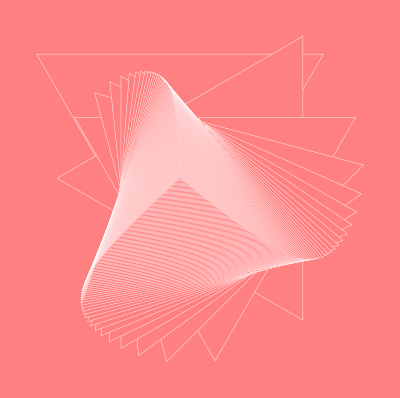

```mathematica
polygonSwirl[
polygon=equilateralTriangle[],
thickness=.3,
depth=100,
color=Pink,
edgeColor=White,
scalingRate=-.0001,
xtranslationRate=-1,
ytranslationRate=-1,
background=Pink,
rotationRate=1,
rotPoint={0,0},
rotModifier=0
]
```